```mathematica
Solve[ Exp[-2 ⅈ Sqrt[2  eng] ](Sqrt[2  eng] - ⅈ  Sqrt[2  (eng - 30)] Cot[Sqrt[2  (eng - 30)]])/(Sqrt[2  eng] + ⅈ  Sqrt[2  (eng - 30)] Cot[Sqrt[2  (eng - 30)]])== -Exp[ⅈ 2 d], d]
```

{{d→ConditionalExpression[-1/2 ⅈ (2 ⅈ π C[1]+Log[-((√2 ⅇ^(-2 ⅈ √2 √eng) √eng)/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)]))+(ⅈ √2 ⅇ^(-2 ⅈ √2 √eng) √(-30+eng) Cot[√2 √(-30+eng)])/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)])]),C[1]∈ℤ]}}

```mathematica
d[eng_]:=-1/2 ⅈ (Log[-(√2 ⅇ^(-2 ⅈ √2 √eng) √eng)/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)])+(ⅈ √2 ⅇ^(-2 ⅈ √2 √eng) √(-30+eng) Cot[√2 √(-30+eng)])/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)])])
```

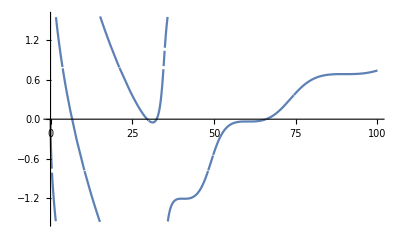

```mathematica
Plot[d[eng],{eng,0,100}]
```

```mathematica
diff[eng_]:=D[d[eng],eng]
```

```mathematica
diff[eng]
```

-((ⅈ ((2 ⅈ ⅇ^(-2 ⅈ √2 √eng))/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)])-ⅇ^(-2 ⅈ √2 √eng)/(√2 √eng (√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)]))+(ⅈ ⅇ^(-2 ⅈ √2 √eng) Cot[√2 √(-30+eng)])/(√2 √(-30+eng) (√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)]))+(2 ⅇ^(-2 ⅈ √2 √eng) √(-30+eng) Cot[√2 √(-30+eng)])/(√eng (√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)]))-(ⅈ ⅇ^(-2 ⅈ √2 √eng) Csc[√2 √(-30+eng)]^2)/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)])+(√2 ⅇ^(-2 ⅈ √2 √eng) √eng (1/(√2 √eng)+(ⅈ Cot[√2 √(-30+eng)])/(√2 √(-30+eng))-ⅈ Csc[√2 √(-30+eng)]^2))/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)])^2-(ⅈ √2 ⅇ^(-2 ⅈ √2 √eng) √(-30+eng) Cot[√2 √(-30+eng)] (1/(√2 √eng)+(ⅈ Cot[√2 √(-30+eng)])/(√2 √(-30+eng))-ⅈ Csc[√2 √(-30+eng)]^2))/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)])^2))/(2 (-(√2 ⅇ^(-2 ⅈ √2 √eng) √eng)/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)])+(ⅈ √2 ⅇ^(-2 ⅈ √2 √eng) √(-30+eng) Cot[√2 √(-30+eng)])/(√2 √eng+ⅈ √2 √(-30+eng) Cot[√2 √(-30+eng)]))))

```mathematica
difff[EE_]:=(ⅈ ⅇ^(2 ⅈ √2 √EE) (√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]) ((ⅈ √2 ⅇ^(-2 ⅈ √2 √EE) (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))/(√EE (√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))+(ⅇ^(-2 ⅈ √2 √EE) (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]) (1/(√2 √EE)+(ⅈ Cot[√2 √(-30+EE)])/(√2 √(-30+EE))-ⅈ Csc[√2 √(-30+EE)]^2))/(√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)])^2-(ⅇ^(-2 ⅈ √2 √EE) (1/(√2 √EE)-(ⅈ Cot[√2 √(-30+EE)])/(√2 √(-30+EE))+ⅈ Csc[√2 √(-30+EE)]^2))/(√2 √EE+ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)])))/(2 (√2 √EE-ⅈ √2 √(-30+EE) Cot[√2 √(-30+EE)]))
```

```mathematica
N[difff[1]]
```

-0.614259+0. ⅈ

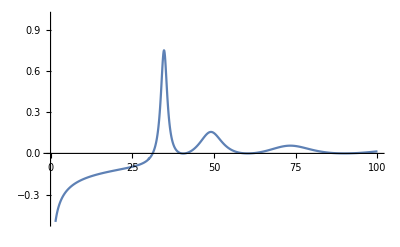

```mathematica
ListLinePlot[Table[{x, N[difff[EE]]/.EE ->x},{x,0.1,100,0.1}],PlotRange-> {-0.5,1}]
```

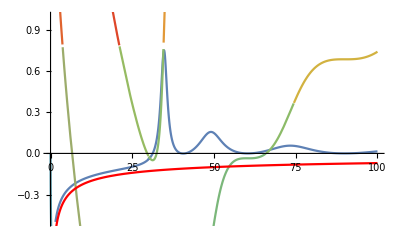

```mathematica
Show[ListLinePlot[Table[{x, N[difff[EE]]/.EE ->x},{x,0.1,100,0.1}],PlotRange-> {-0.5,1}],Plot[d[eng],{eng,0,100},ColorFunction->"Rainbow"],Plot[-1/(Sqrt[2eng]),{eng,0,100},ColorFunction->Hue,PlotRange->All]]
```

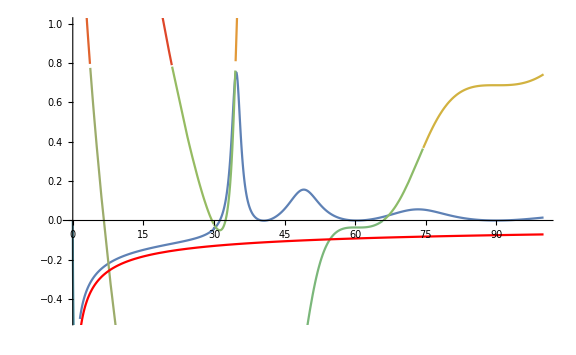

```mathematica
Show[%14,ImageSize->Large]
```